```mathematica
CheckPSP[h_][l_,S_,E_,Flag_]:=Module[{i,list={},c=S-1,result=0},
For[i=S,i≤E, i++,
list=FrobeniusSolve[l,i];
list=Plus@@@list;
If[Min[list]>h,Break[],c=c+1;If[Mod[c,3]==0&&Flag==1,Print[c]];];
];
c
]
```

```mathematica
Current Results
3->15
4->44
5->126
6->388
7->1137
8->3485
```

```mathematica
FIB Results
3->12
4->33
5->88
6->232
7->609
8->1596
```

```mathematica
My table {a,r}
{3,2.2}
{2.5,2.5}
```

```mathematica
Flist:={1}∪Table[LucasL[i],{i,2,20,2}]


Flist3:={1,4,10,23,57,132,301,701};

f1[a_,r_][j_]:=Floor[a*r^(j-1)];



Flist11:={1}∪Table[f1[4,2.2][j],{j,1,10}];
Print[Flist3];
For[i=7,i≤7,i++,Print[CheckPSP[i][Flist3[[1;;i]],590,615,1] ];]
```

{1,4,10,23,57,132,301,701}

591

594

597

600

600

```mathematica
Module[{a,r,l1,l2,l3={}},
For[a=1.6,a≤4.6,a=a+0.05,
For[r=2.2,r≤2.6,r=r+0.05,
l1={1}∪Table[f1[a,r][j],{j,1,6}];
l2={};
For[i=3,i≤6,i++,
AppendTo[l2,
CheckPSP[i][l1[[1;;i]]]];
];
AppendTo[l3,{a,r,l1}->l2];
Print[{a,r,l1}->l2];
];
];
l3
]
```

{1.6,2.2,{1,3,7,17,37,82}}→{11,28,65,222}

{1.6,2.25,{1,3,8,18,41,92}}→{12,30,73,239}

{1.6,2.3,{1,3,8,19,44,102}}→{12,33,77,182}

{1.6,2.35,{1,3,8,20,48,114}}→{12,32,85,206}

{1.6,2.4,{1,3,9,22,53,127}}→{7,16,91,218}

{1.6,2.45,{1,3,9,23,57,141}}→{7,16,39,96}

{1.6,2.5,{1,3,9,24,62,156}}→{7,16,40,102}

{1.6,2.55,{1,4,10,26,67,172}}→{6,16,42,109}

{1.6,2.6,{1,4,10,28,73,190}}→{6,16,26,54}

{1.65,2.2,{1,3,7,17,38,85}}→{11,28,66,219}

{1.65,2.25,{1,3,8,18,42,95}}→{12,30,82,177}

{1.65,2.3,{1,3,8,20,46,106}}→{12,32,78,196}

{1.65,2.35,{1,3,9,21,50,118}}→{7,16,37,196}

{1.65,2.4,{1,3,9,22,54,131}}→{7,16,91,222}

{1.65,2.45,{1,4,9,24,59,145}}→{6,38,97,242}

{1.65,2.5,{1,4,10,25,64,161}}→{6,16,41,105}

{1.65,2.55,{1,4,10,27,69,177}}→{6,16,52,229}

{1.65,2.6,{1,4,11,29,75,196}}→{6,17,46,121}

{1.7,2.2,{1,3,8,18,39,87}}→{12,30,102,237}

{1.7,2.25,{1,3,8,19,43,98}}→{12,33,79,251}

{1.7,2.3,{1,3,8,20,47,109}}→{12,32,81,279}

{1.7,2.35,{1,3,9,22,51,121}}→{7,16,89,210}

{1.7,2.4,{1,4,9,23,56,135}}→{6,29,52,108}

{1.7,2.45,{1,4,10,25,61,150}}→{6,16,41,102}

{1.7,2.5,{1,4,10,26,66,166}}→{6,16,42,124}

{1.7,2.55,{1,4,11,28,71,183}}→{6,17,45,136}

{1.7,2.6,{1,4,11,29,77,201}}→{6,17,46,75}

{1.75,2.2,{1,3,8,18,40,90}}→{12,30,70,232}

{1.75,2.25,{1,3,8,19,44,100}}→{12,33,77,180}

{1.75,2.3,{1,4,9,21,48,112}}→{6,36,88,291}

{1.75,2.35,{1,4,9,22,53,125}}→{6,28,50,103}

{1.75,2.4,{1,4,10,24,58,139}}→{6,16,46,104}

{1.75,2.45,{1,4,10,25,63,154}}→{6,16,41,258}

{1.75,2.5,{1,4,10,27,68,170}}→{6,16,52,120}

{1.75,2.55,{1,4,11,29,73,188}}→{6,17,46,122}

{1.75,2.6,{1,4,11,30,79,207}}→{6,17,28,107}

{1.8,2.2,{1,3,8,19,42,92}}→{12,33,96,238}

{1.8,2.25,{1,4,9,20,46,103}}→{6,34,107,267}

{1.8,2.3,{1,4,9,21,50,115}}→{6,36,86,205}

{1.8,2.35,{1,4,9,23,54,129}}→{6,29,52,106}

{1.8,2.4,{1,4,10,24,59,143}}→{6,16,46,244}

{1.8,2.45,{1,4,10,26,64,158}}→{6,16,42,106}

{1.8,2.5,{1,4,11,28,70,175}}→{6,17,45,118}

{1.8,2.55,{1,4,11,29,76,194}}→{6,17,46,122}

{1.8,2.6,{1,4,12,31,82,213}}→{6,10,22,53}

{1.85,2.2,{1,4,8,19,43,95}}→{6,14,33,230}

{1.85,2.25,{1,4,9,21,47,106}}→{6,36,91,206}

{1.85,2.3,{1,4,9,22,51,119}}→{6,28,79,198}

{1.85,2.35,{1,4,10,24,56,132}}→{6,16,46,102}

{1.85,2.4,{1,4,10,25,61,147}}→{6,16,41,102}

{1.85,2.45,{1,4,11,27,66,163}}→{6,17,51,117}

{1.85,2.5,{1,4,11,28,72,180}}→{6,17,45,117}

{1.85,2.55,{1,4,12,30,78,199}}→{6,10,22,100}

{1.85,2.6,{1,4,12,32,84,219}}→{6,10,22,54}

{1.9,2.2,{1,4,9,20,44,97}}→{6,34,78,260}

{1.9,2.25,{1,4,9,21,48,109}}→{6,36,88,197}

{1.9,2.3,{1,4,10,23,53,122}}→{6,16,94,226}

{1.9,2.35,{1,4,10,24,57,136}}→{6,16,46,233}

{1.9,2.4,{1,4,10,26,63,151}}→{6,16,42,121}

{1.9,2.45,{1,4,11,27,68,167}}→{6,17,51,281}

{1.9,2.5,{1,4,11,29,74,185}}→{6,17,46,138}

{1.9,2.55,{1,4,12,31,80,204}}→{6,10,22,53}

{1.9,2.6,{1,4,12,33,86,225}}→{6,10,22,108}

{1.95,2.2,{1,4,9,20,45,100}}→{6,34,87,196}

{1.95,2.25,{1,4,9,22,49,112}}→{6,28,77,189}

{1.95,2.3,{1,4,10,23,54,125}}→{6,16,89,214}

{1.95,2.35,{1,4,10,25,59,139}}→{6,16,41,106}

{1.95,2.4,{1,4,11,26,64,155}}→{6,17,46,261}

{1.95,2.45,{1,4,11,28,70,172}}→{6,17,45,118}

{1.95,2.5,{1,4,12,30,76,190}}→{6,10,22,128}

{1.95,2.55,{1,4,12,32,82,210}}→{6,10,22,54}

{1.95,2.6,{1,5,13,34,89,231}}→{3,8,21,55}

{2.,2.2,{1,2,4,9,21,46,103}}→{10,24,57,128}

{2.,2.25,{1,2,4,10,22,51,115}}→{10,26,60,181}

{2.,2.3,{1,2,4,10,24,55,128}}→{10,26,64,156}

{2.,2.35,{1,2,4,11,25,60,143}}→{10,28,67,162}

{2.,2.4,{1,2,4,11,27,66,159}}→{10,28,71,176}

{2.,2.45,{1,2,4,12,29,72,176}}→{10,22,78,193}

{2.,2.5,{1,2,4,12,31,78,195}}→{10,22,53,150}

{2.,2.55,{1,2,5,13,33,84,215}}→{12,33,86,221}

{2.,2.6,{1,2,5,13,35,91,237}}→{12,33,68,159}

{2.05,2.2,{1,2,4,9,21,48,105}}→{10,24,57,171}

{2.05,2.25,{1,2,4,10,23,52,118}}→{10,26,64,187}

{2.05,2.3,{1,2,4,10,24,57,131}}→{10,26,64,160}

{2.05,2.35,{1,2,4,11,26,62,146}}→{10,28,71,170}

{2.05,2.4,{1,2,4,11,28,68,163}}→{10,28,73,184}

{2.05,2.45,{1,2,5,12,30,73,180}}→{12,31,79,195}

{2.05,2.5,{1,2,5,12,32,80,200}}→{12,31,83,211}

{2.05,2.55,{1,2,5,13,33,86,221}}→{12,33,86,225}

{2.05,2.6,{1,2,5,13,36,93,243}}→{12,33,69,162}

{2.1,2.2,{1,2,4,10,22,49,108}}→{10,26,60,175}

{2.1,2.25,{1,2,4,10,23,53,121}}→{10,26,64,147}

{2.1,2.3,{1,2,4,11,25,58,135}}→{10,28,67,160}

{2.1,2.35,{1,2,4,11,27,64,150}}→{10,28,71,174}

{2.1,2.4,{1,2,5,12,29,69,167}}→{12,31,77,187}

{2.1,2.45,{1,2,5,12,30,75,185}}→{12,31,79,200}

{2.1,2.5,{1,2,5,13,32,82,205}}→{12,33,84,216}

{2.1,2.55,{1,2,5,13,34,88,226}}→{12,33,88,230}

{2.1,2.6,{1,2,5,14,36,95,249}}→{12,26,62,188}

{2.15,2.2,{1,2,4,10,22,50,110}}→{10,26,60,140}

{2.15,2.25,{1,2,4,10,24,55,123}}→{10,26,64,156}

{2.15,2.3,{1,2,4,11,26,60,138}}→{10,28,71,166}

{2.15,2.35,{1,2,5,11,27,65,154}}→{12,29,72,175}

{2.15,2.4,{1,2,5,12,29,71,171}}→{12,31,77,190}

{2.15,2.45,{1,2,5,12,31,77,189}}→{12,31,81,204}

{2.15,2.5,{1,2,5,13,33,83,209}}→{12,33,86,220}

{2.15,2.55,{1,2,5,13,35,90,231}}→{12,33,68,158}

{2.15,2.6,{1,2,5,14,37,98,255}}→{12,26,63,170}

{2.2,2.2,{1,2,4,10,23,51,113}}→{10,26,64,169}

{2.2,2.25,{1,2,4,11,25,56,126}}→{10,28,67,154}

{2.2,2.3,{1,2,5,11,26,61,141}}→{12,29,70,167}

{2.2,2.35,{1,2,5,12,28,67,157}}→{12,31,76,182}

{2.2,2.4,{1,2,5,12,30,72,175}}→{12,31,79,194}

{2.2,2.45,{1,2,5,13,32,79,194}}→{12,33,84,210}

{2.2,2.5,{1,2,5,13,34,85,214}}→{12,33,88,224}

{2.2,2.55,{1,2,5,14,36,93,237}}→{12,26,62,155}

{2.2,2.6,{1,2,5,14,38,100,261}}→{12,26,64,164}

{2.25,2.2,{1,2,4,10,23,52,115}}→{10,26,64,187}

{2.25,2.25,{1,2,5,11,25,57,129}}→{12,29,69,204}

{2.25,2.3,{1,2,5,11,27,62,144}}→{12,29,72,175}

{2.25,2.35,{1,2,5,12,29,68,161}}→{12,31,77,187}

{2.25,2.4,{1,2,5,12,31,74,179}}→{12,31,81,201}

{2.25,2.45,{1,2,5,13,33,81,198}}→{12,33,86,215}

{2.25,2.5,{1,2,5,14,35,87,219}}→{12,26,61,148}

{2.25,2.55,{1,2,5,14,37,95,242}}→{12,26,63,158}

{2.25,2.6,{1,2,5,15,39,102,267}}→{12,27,66,168}

{2.3,2.2,{1,2,5,11,24,53,118}}→{12,29,66,190}

{2.3,2.25,{1,2,5,11,26,58,132}}→{12,29,70,160}

{2.3,2.3,{1,2,5,12,27,64,148}}→{12,31,73,174}

{2.3,2.35,{1,2,5,12,29,70,164}}→{12,31,77,188}

{2.3,2.4,{1,2,5,13,31,76,183}}→{12,33,83,206}

{2.3,2.45,{1,2,5,13,33,82,203}}→{12,33,86,217}

{2.3,2.5,{1,2,5,14,35,89,224}}→{12,26,61,150}

{2.3,2.55,{1,2,5,14,38,97,247}}→{12,26,64,171}

{2.3,2.6,{1,2,5,15,40,105,273}}→{12,27,67,172}

{2.35,2.2,{1,2,5,11,25,55,121}}→{12,29,69,183}

{2.35,2.25,{1,2,5,11,26,60,135}}→{12,29,70,170}

{2.35,2.3,{1,2,5,12,28,65,151}}→{12,31,76,180}

{2.35,2.35,{1,2,5,12,30,71,168}}→{12,31,79,194}

{2.35,2.4,{1,2,5,13,32,77,187}}→{12,33,84,207}

{2.35,2.45,{1,2,5,14,34,84,207}}→{12,26,90,194}

{2.35,2.5,{1,2,5,14,36,91,229}}→{12,26,62,175}

{2.35,2.55,{1,2,5,15,38,99,253}}→{12,27,65,164}

{2.35,2.6,{1,2,6,15,41,107,279}}→{10,25,66,173}

{2.4,2.2,{1,2,5,11,25,56,123}}→{12,29,69,201}

{2.4,2.25,{1,2,5,12,27,61,138}}→{12,31,73,171}

{2.4,2.3,{1,2,5,12,29,67,154}}→{12,31,77,185}

{2.4,2.35,{1,2,5,13,31,73,172}}→{12,33,83,200}

{2.4,2.4,{1,2,5,13,33,79,191}}→{12,33,86,214}

{2.4,2.45,{1,2,5,14,35,86,211}}→{12,26,61,147}

{2.4,2.5,{1,2,5,14,37,93,234}}→{12,26,63,156}

{2.4,2.55,{1,2,6,15,39,101,258}}→{10,25,64,165}

{2.4,2.6,{1,2,6,16,42,109,285}}→{10,26,68,177}

{2.45,2.2,{1,2,5,11,26,57,126}}→{12,29,70,158}

{2.45,2.25,{1,2,5,12,27,62,141}}→{12,31,73,173}

{2.45,2.3,{1,2,5,12,29,68,157}}→{12,31,77,187}

{2.45,2.35,{1,2,5,13,31,74,175}}→{12,33,83,200}

{2.45,2.4,{1,2,5,14,33,81,195}}→{12,26,59,216}

{2.45,2.45,{1,2,6,14,36,88,216}}→{10,24,60,148}

{2.45,2.5,{1,2,6,15,38,95,239}}→{10,25,63,251}

{2.45,2.55,{1,2,6,15,40,103,264}}→{10,25,78,181}

{2.45,2.6,{1,2,6,16,43,111,291}}→{10,26,73,184}

{2.5,2.2,{1,2,5,12,26,58,128}}→{12,31,71,164}

{2.5,2.25,{1,2,5,12,28,64,144}}→{12,31,76,178}

{2.5,2.3,{1,2,5,13,30,69,160}}→{12,33,80,191}

{2.5,2.35,{1,2,5,13,32,76,179}}→{12,33,84,207}

{2.5,2.4,{1,2,5,14,34,82,199}}→{12,26,90,220}

{2.5,2.45,{1,2,6,15,36,90,220}}→{10,25,70,240}

{2.5,2.5,{1,2,6,15,39,97,244}}→{10,25,64,256}

{2.5,2.55,{1,2,6,16,41,105,269}}→{10,26,67,172}

{2.5,2.6,{1,2,6,16,43,114,297}}→{10,26,73,197}

{2.55,2.2,{1,2,5,12,27,59,131}}→{12,31,73,164}

{2.55,2.25,{1,2,5,12,29,65,147}}→{12,31,77,178}

{2.55,2.3,{1,2,5,13,31,71,164}}→{12,33,83,197}

{2.55,2.35,{1,2,5,14,33,77,182}}→{12,26,59,199}

{2.55,2.4,{1,2,6,14,35,84,203}}→{10,24,59,164}

{2.55,2.45,{1,2,6,15,37,91,225}}→{10,25,62,175}

{2.55,2.5,{1,2,6,15,39,99,249}}→{10,25,64,187}

{2.55,2.55,{1,2,6,16,42,107,274}}→{10,26,68,201}

{2.55,2.6,{1,2,6,17,44,116,302}}→{10,27,71,191}

{2.6,2.2,{1,2,5,12,27,60,133}}→{12,31,73,166}

{2.6,2.25,{1,2,5,13,29,66,149}}→{12,33,78,184}

{2.6,2.3,{1,2,5,13,31,72,167}}→{12,33,83,198}

{2.6,2.35,{1,2,6,14,33,79,186}}→{10,24,84,182}

{2.6,2.4,{1,2,6,14,35,86,207}}→{10,24,59,166}

{2.6,2.45,{1,2,6,15,38,93,229}}→{10,25,63,156}

{2.6,2.5,{1,2,6,16,40,101,253}}→{10,26,66,195}

{2.6,2.55,{1,2,6,16,43,109,280}}→{10,26,73,182}

{2.6,2.6,{1,2,6,17,45,118,308}}→{10,27,72,190}

{2.65,2.2,{1,2,5,12,28,62,136}}→{12,31,76,172}

{2.65,2.25,{1,2,5,13,30,67,152}}→{12,33,80,184}

{2.65,2.3,{1,2,6,14,32,74,170}}→{10,24,82,198}

{2.65,2.35,{1,2,6,14,34,80,189}}→{10,24,58,146}

{2.65,2.4,{1,2,6,15,36,87,211}}→{10,25,70,157}

{2.65,2.45,{1,2,6,15,38,95,233}}→{10,25,63,251}

{2.65,2.5,{1,2,6,16,41,103,258}}→{10,26,67,174}

{2.65,2.55,{1,2,6,17,43,112,285}}→{10,27,70,182}

{2.65,2.6,{1,2,6,17,46,121,314}}→{10,27,44,165}

{2.7,2.2,{1,2,5,13,28,63,139}}→{12,33,76,178}

{2.7,2.25,{1,2,6,13,30,69,155}}→{10,34,82,191}

{2.7,2.3,{1,2,6,14,32,75,173}}→{10,24,82,200}

{2.7,2.35,{1,2,6,14,35,82,193}}→{10,24,59,149}

{2.7,2.4,{1,2,6,15,37,89,214}}→{10,25,62,160}

{2.7,2.45,{1,2,6,16,39,97,238}}→{10,26,75,224}

{2.7,2.5,{1,2,6,16,42,105,263}}→{10,26,68,177}

{2.7,2.55,{1,2,6,17,44,114,291}}→{10,27,71,185}

{2.7,2.6,{1,2,7,18,47,123,320}}→{11,29,76,199}

{2.75,2.2,{1,2,6,13,29,64,141}}→{10,34,79,178}

{2.75,2.25,{1,2,6,13,31,70,158}}→{10,34,72,192}

{2.75,2.3,{1,2,6,14,33,76,176}}→{10,24,84,203}

{2.75,2.35,{1,2,6,15,35,83,197}}→{10,25,89,220}

{2.75,2.4,{1,2,6,15,38,91,218}}→{10,25,63,177}

{2.75,2.45,{1,2,6,16,40,99,242}}→{10,26,66,169}

{2.75,2.5,{1,2,6,17,42,107,268}}→{10,27,74,181}

{2.75,2.55,{1,2,7,17,45,116,296}}→{11,28,73,189}

{2.75,2.6,{1,2,7,18,48,125,326}}→{11,29,77,202}

{2.8,2.2,{1,2,6,13,29,65,144}}→{10,34,79,192}

{2.8,2.25,{1,2,6,14,31,71,161}}→{10,24,80,199}

{2.8,2.3,{1,2,6,14,34,78,180}}→{10,24,58,144}

{2.8,2.35,{1,2,6,15,36,85,200}}→{10,25,70,225}

{2.8,2.4,{1,2,6,16,38,92,222}}→{10,26,68,160}

{2.8,2.45,{1,2,6,16,41,100,247}}→{10,26,67,177}

{2.8,2.5,{1,2,6,17,43,109,273}}→{10,27,70,184}

{2.8,2.55,{1,2,7,18,46,118,301}}→{11,29,75,193}

{2.8,2.6,{1,2,7,18,49,127,332}}→{11,29,47,174}

{2.85,2.2,{1,2,6,13,30,66,146}}→{10,34,82,184}

{2.85,2.25,{1,2,6,14,32,73,164}}→{10,24,82,204}

{2.85,2.3,{1,2,6,15,34,79,183}}→{10,25,87,211}

{2.85,2.35,{1,2,6,15,36,86,204}}→{10,25,70,156}

{2.85,2.4,{1,2,6,16,39,94,226}}→{10,26,75,169}

{2.85,2.45,{1,2,6,17,41,102,251}}→{10,27,72,174}

{2.85,2.5,{1,2,7,17,44,111,278}}→{11,28,72,210}

{2.85,2.55,{1,2,7,18,47,120,307}}→{11,29,76,197}

{2.85,2.6,{1,2,7,19,50,130,338}}→{11,30,80,210}

{2.9,2.2,{1,2,6,14,30,67,149}}→{10,24,54,174}

{2.9,2.25,{1,2,6,14,33,74,167}}→{10,24,84,199}

{2.9,2.3,{1,2,6,15,35,81,186}}→{10,25,89,216}

{2.9,2.35,{1,2,6,16,37,88,207}}→{10,26,67,227}

{2.9,2.4,{1,2,6,16,40,96,230}}→{10,26,66,172}

{2.9,2.45,{1,2,7,17,42,104,255}}→{11,28,70,199}

{2.9,2.5,{1,2,7,18,45,113,283}}→{11,29,74,192}

{2.9,2.55,{1,2,7,18,48,122,312}}→{11,29,77,204}

{2.9,2.6,{1,2,7,19,50,132,344}}→{11,30,80,130}

{2.95,2.2,{1,2,6,14,31,69,152}}→{10,24,80,187}

{2.95,2.25,{1,2,6,14,33,75,170}}→{10,24,84,209}

{2.95,2.3,{1,2,6,15,35,82,189}}→{10,25,89,218}

{2.95,2.35,{1,2,6,16,38,89,211}}→{10,26,68,230}

{2.95,2.4,{1,2,7,16,40,97,234}}→{11,28,68,165}

{2.95,2.45,{1,2,7,17,43,106,260}}→{11,28,71,177}

{2.95,2.5,{1,2,7,18,46,115,288}}→{11,29,75,195}

{2.95,2.55,{1,2,7,19,48,124,318}}→{11,30,78,202}

{2.95,2.6,{1,2,7,19,51,134,350}}→{11,30,49,100}

{3.,2.2,{1,2,6,14,31,70,154}}→{10,24,80,189}

{3.,2.25,{1,2,6,15,34,76,172}}→{10,25,87,205}

{3.,2.3,{1,2,6,15,36,83,193}}→{10,25,70,153}

{3.,2.35,{1,2,7,16,38,91,215}}→{11,28,66,157}

{3.,2.4,{1,2,7,17,41,99,238}}→{11,28,70,169}

{3.,2.45,{1,2,7,18,44,108,264}}→{11,29,74,192}

{3.,2.5,{1,2,7,18,46,117,292}}→{11,29,75,193}

{3.,2.55,{1,2,7,19,49,126,323}}→{11,30,79,205}

{3.,2.6,{1,2,7,20,52,137,356}}→{11,18,38,90}

{3.05,2.2,{1,3,6,14,32,71,157}}→{10,24,82,192}

{3.05,2.25,{1,3,6,15,34,78,175}}→{10,25,87,212}

{3.05,2.3,{1,3,7,16,37,85,196}}→{11,40,98,231}

{3.05,2.35,{1,3,7,16,39,93,218}}→{11,40,104,252}

{3.05,2.4,{1,3,7,17,42,101,242}}→{11,28,80,265}

{3.05,2.45,{1,3,7,18,44,109,269}}→{11,29,73,186}

{3.05,2.5,{1,3,7,19,47,119,297}}→{11,30,77,196}

{3.05,2.55,{1,3,7,19,50,128,328}}→{11,30,80,208}

{3.05,2.6,{1,3,7,20,53,139,362}}→{11,18,38,91}

{3.1,2.2,{1,3,6,15,33,72,159}}→{10,25,58,130}

{3.1,2.25,{1,3,6,15,35,79,178}}→{10,25,63,206}

{3.1,2.3,{1,3,7,16,37,86,199}}→{11,40,98,237}

{3.1,2.35,{1,3,7,17,40,94,222}}→{11,28,72,172}

{3.1,2.4,{1,3,7,17,42,102,246}}→{11,28,80,182}

{3.1,2.45,{1,3,7,18,45,111,273}}→{11,29,85,196}

{3.1,2.5,{1,3,7,19,48,121,302}}→{11,30,84,234}

{3.1,2.55,{1,3,7,20,51,131,334}}→{11,18,38,219}

{3.1,2.6,{1,3,8,20,54,141,368}}→{12,32,52,106}

{3.15,2.2,{1,3,6,15,33,73,162}}→{10,25,58,198}

{3.15,2.25,{1,3,7,15,35,80,181}}→{11,26,61,218}

{3.15,2.3,{1,3,7,16,38,88,202}}→{11,40,87,225}

{3.15,2.35,{1,3,7,17,40,96,225}}→{11,28,72,168}

{3.15,2.4,{1,3,7,18,43,104,250}}→{11,29,76,180}

{3.15,2.45,{1,3,7,18,46,113,278}}→{11,29,75,188}

{3.15,2.5,{1,3,7,19,49,123,307}}→{11,30,79,206}

{3.15,2.55,{1,3,8,20,52,133,339}}→{12,32,84,217}

{3.15,2.6,{1,3,8,21,55,143,374}}→{12,33,88,231}

{3.2,2.2,{1,3,7,15,34,74,164}}→{11,26,87,201}

{3.2,2.25,{1,3,7,16,36,82,184}}→{11,40,96,224}

{3.2,2.3,{1,3,7,16,38,89,205}}→{11,40,87,176}

{3.2,2.35,{1,3,7,17,41,97,229}}→{11,28,69,176}

{3.2,2.4,{1,3,7,18,44,106,254}}→{11,29,73,190}

{3.2,2.45,{1,3,7,19,47,115,282}}→{11,30,77,192}

{3.2,2.5,{1,3,7,19,49,124,312}}→{11,30,79,207}

{3.2,2.55,{1,3,8,20,53,135,345}}→{12,32,85,225}

{3.2,2.6,{1,3,8,21,56,146,380}}→{12,33,54,110}

{3.25,2.2,{1,3,7,15,34,76,167}}→{11,26,87,205}

{3.25,2.25,{1,3,7,16,37,83,187}}→{11,40,98,227}

{3.25,2.3,{1,3,7,17,39,90,209}}→{11,28,71,234}

{3.25,2.35,{1,3,7,17,42,99,232}}→{11,28,80,179}

{3.25,2.4,{1,3,7,18,44,107,258}}→{11,29,73,180}

{3.25,2.45,{1,3,7,19,47,117,286}}→{11,30,77,198}

{3.25,2.5,{1,3,8,20,50,126,317}}→{12,32,84,240}

{3.25,2.55,{1,3,8,21,53,137,350}}→{12,33,88,225}

{3.25,2.6,{1,3,8,21,57,148,386}}→{12,33,54,111}

{3.3,2.2,{1,3,7,15,35,77,170}}→{11,26,61,138}

{3.3,2.25,{1,3,7,16,37,84,190}}→{11,40,98,229}

{3.3,2.3,{1,3,7,17,40,92,212}}→{11,28,72,164}

{3.3,2.35,{1,3,7,18,42,100,236}}→{11,29,75,182}

{3.3,2.4,{1,3,7,19,45,109,262}}→{11,30,79,188}

{3.3,2.45,{1,3,8,19,48,118,291}}→{12,33,81,226}

{3.3,2.5,{1,3,8,20,51,128,322}}→{12,32,83,213}

{3.3,2.55,{1,3,8,21,54,139,355}}→{12,33,87,228}

{3.3,2.6,{1,3,8,22,58,150,392}}→{12,20,42,100}

{3.35,2.2,{1,3,7,16,35,78,172}}→{11,40,81,202}

{3.35,2.25,{1,3,7,16,38,85,193}}→{11,40,87,219}

{3.35,2.3,{1,3,7,17,40,93,215}}→{11,28,72,171}

{3.35,2.35,{1,3,7,18,43,102,240}}→{11,29,76,262}

{3.35,2.4,{1,3,8,19,46,111,266}}→{12,33,79,190}

{3.35,2.45,{1,3,8,20,49,120,295}}→{12,32,81,213}

{3.35,2.5,{1,3,8,20,52,130,327}}→{12,32,84,214}

{3.35,2.55,{1,3,8,21,55,141,361}}→{12,33,88,229}

{3.35,2.6,{1,3,8,22,58,153,398}}→{12,20,42,100}

{3.4,2.2,{1,3,7,16,36,79,175}}→{11,40,96,220}

{3.4,2.25,{1,3,7,17,38,87,196}}→{11,28,66,223}

{3.4,2.3,{1,3,7,17,41,95,218}}→{11,28,69,168}

{3.4,2.35,{1,3,7,18,44,103,243}}→{11,29,73,180}

{3.4,2.4,{1,3,8,19,47,112,270}}→{12,33,80,192}

{3.4,2.45,{1,3,8,20,50,122,300}}→{12,32,84,206}

{3.4,2.5,{1,3,8,21,53,132,332}}→{12,33,88,225}

{3.4,2.55,{1,3,8,22,56,143,366}}→{12,20,42,235}

{3.4,2.6,{1,3,8,22,59,155,403}}→{12,20,42,101}

{3.45,2.2,{1,3,7,16,36,80,177}}→{11,40,96,220}

{3.45,2.25,{1,3,7,17,39,88,198}}→{11,28,71,230}

{3.45,2.3,{1,3,7,18,41,96,222}}→{11,29,70,189}

{3.45,2.35,{1,3,8,19,44,105,247}}→{12,33,77,182}

{3.45,2.4,{1,3,8,19,47,114,274}}→{12,33,80,194}

{3.45,2.45,{1,3,8,20,50,124,304}}→{12,32,84,218}

{3.45,2.5,{1,3,8,21,53,134,336}}→{12,33,88,254}

{3.45,2.55,{1,3,8,22,57,145,371}}→{12,20,42,99}

{3.45,2.6,{1,3,8,23,60,157,409}}→{12,20,43,103}

{3.5,2.2,{1,3,7,16,37,81,180}}→{11,40,98,226}

{3.5,2.25,{1,3,7,17,39,89,201}}→{11,28,71,160}

{3.5,2.3,{1,3,8,18,42,97,225}}→{12,30,82,260}

{3.5,2.35,{1,3,8,19,45,106,250}}→{12,33,81,245}

{3.5,2.4,{1,3,8,20,48,116,278}}→{12,32,85,201}

{3.5,2.45,{1,3,8,21,51,126,308}}→{12,33,89,223}

{3.5,2.5,{1,3,8,21,54,136,341}}→{12,33,87,225}

{3.5,2.55,{1,3,8,22,58,147,377}}→{12,20,42,100}

{3.5,2.6,{1,3,9,23,61,159,415}}→{7,16,39,120}

{3.55,2.2,{1,3,7,17,37,83,182}}→{11,28,65,152}

{3.55,2.25,{1,3,7,17,40,90,204}}→{11,28,72,168}

{3.55,2.3,{1,3,8,18,43,99,228}}→{12,30,73,255}

{3.55,2.35,{1,3,8,19,46,108,254}}→{12,33,79,190}

{3.55,2.4,{1,3,8,20,49,117,282}}→{12,32,81,200}

{3.55,2.45,{1,3,8,21,52,127,313}}→{12,33,85,212}

{3.55,2.5,{1,3,8,22,55,138,346}}→{12,20,42,97}

{3.55,2.55,{1,3,9,23,58,150,382}}→{7,16,39,111}

{3.55,2.6,{1,3,9,23,62,162,421}}→{7,16,39,121}

{3.6,2.2,{1,3,7,17,38,84,185}}→{11,28,66,233}

{3.6,2.25,{1,3,8,18,41,92,207}}→{12,30,73,239}

{3.6,2.3,{1,3,8,19,43,100,231}}→{12,33,79,260}

{3.6,2.35,{1,3,8,19,46,109,258}}→{12,33,79,188}

{3.6,2.4,{1,3,8,20,49,119,286}}→{12,32,81,200}

{3.6,2.45,{1,3,8,21,52,129,317}}→{12,33,85,214}

{3.6,2.5,{1,3,8,22,56,140,351}}→{12,20,42,182}

{3.6,2.55,{1,3,9,23,59,152,388}}→{7,16,39,98}

{3.6,2.6,{1,3,9,24,63,164,427}}→{7,16,40,103}

{3.65,2.2,{1,3,8,17,38,85,188}}→{12,29,90,222}

{3.65,2.25,{1,3,8,18,41,93,210}}→{12,30,73,249}

{3.65,2.3,{1,3,8,19,44,102,234}}→{12,33,77,182}

{3.65,2.35,{1,3,8,20,47,111,261}}→{12,32,81,192}

{3.65,2.4,{1,3,8,21,50,121,290}}→{12,33,85,206}

{3.65,2.45,{1,3,8,21,53,131,322}}→{12,33,88,224}

{3.65,2.5,{1,3,9,22,57,142,356}}→{7,16,73,130}

{3.65,2.55,{1,3,9,23,60,154,393}}→{7,16,39,99}

{3.65,2.6,{1,3,9,24,64,166,433}}→{7,16,40,110}

{3.7,2.2,{1,3,8,17,39,86,190}}→{12,29,99,201}

{3.7,2.25,{1,3,8,18,42,94,213}}→{12,30,82,218}

{3.7,2.3,{1,3,8,19,45,103,238}}→{12,33,81,184}

{3.7,2.35,{1,3,8,20,48,112,265}}→{12,32,85,204}

{3.7,2.4,{1,3,8,21,51,122,294}}→{12,33,89,221}

{3.7,2.45,{1,3,9,22,54,133,326}}→{7,16,91,228}

{3.7,2.5,{1,3,9,23,57,144,361}}→{7,16,39,96}

{3.7,2.55,{1,3,9,24,61,156,398}}→{7,16,40,116}

{3.7,2.6,{1,3,9,25,65,169,439}}→{7,16,41,106}

{3.75,2.2,{1,3,8,18,39,87,193}}→{12,30,102,237}

{3.75,2.25,{1,3,8,18,42,96,216}}→{12,30,82,256}

{3.75,2.3,{1,3,8,19,45,104,241}}→{12,33,81,270}

{3.75,2.35,{1,3,8,20,48,114,268}}→{12,32,85,206}

{3.75,2.4,{1,3,8,21,51,124,298}}→{12,33,89,213}

{3.75,2.45,{1,3,9,22,55,135,331}}→{7,16,92,227}

{3.75,2.5,{1,3,9,23,58,146,366}}→{7,16,39,111}

{3.75,2.55,{1,3,9,24,62,158,404}}→{7,16,40,102}

{3.75,2.6,{1,3,9,25,65,171,445}}→{7,16,41,106}

{3.8,2.2,{1,3,8,18,40,89,195}}→{12,30,70,230}

{3.8,2.25,{1,3,8,19,43,97,219}}→{12,33,79,176}

{3.8,2.3,{1,3,8,20,46,106,244}}→{12,32,78,196}

{3.8,2.35,{1,3,8,20,49,115,272}}→{12,32,81,208}

{3.8,2.4,{1,3,9,21,52,126,302}}→{7,16,37,214}

{3.8,2.45,{1,3,9,22,55,136,335}}→{7,16,92,253}

{3.8,2.5,{1,3,9,23,59,148,371}}→{7,16,39,98}

{3.8,2.55,{1,3,9,24,63,160,409}}→{7,16,40,103}

{3.8,2.6,{1,3,9,25,66,173,451}}→{7,16,41,107}

{3.85,2.2,{1,3,8,18,40,90,198}}→{12,30,70,232}

{3.85,2.25,{1,3,8,19,43,98,222}}→{12,33,79,251}

{3.85,2.3,{1,3,8,20,46,107,247}}→{12,32,78,190}

{3.85,2.35,{1,3,9,21,49,117,275}}→{7,16,37,154}

{3.85,2.4,{1,3,9,22,53,127,306}}→{7,16,91,218}

{3.85,2.45,{1,3,9,23,56,138,339}}→{7,16,39,244}

{3.85,2.5,{1,3,9,24,60,150,375}}→{7,16,40,100}

{3.85,2.55,{1,3,9,25,63,162,415}}→{7,16,41,104}

{3.85,2.6,{1,3,10,26,67,175,457}}→{7,17,43,110}

{3.9,2.2,{1,3,8,18,41,91,200}}→{12,30,73,237}

{3.9,2.25,{1,3,8,19,44,99,224}}→{12,33,77,256}

{3.9,2.3,{1,3,8,20,47,109,251}}→{12,32,81,279}

{3.9,2.35,{1,3,9,21,50,118,279}}→{7,16,37,196}

{3.9,2.4,{1,3,9,22,53,129,310}}→{7,16,91,232}

{3.9,2.45,{1,3,9,23,57,140,344}}→{7,16,39,96}

{3.9,2.5,{1,3,9,24,60,152,380}}→{7,16,40,100}

{3.9,2.55,{1,3,9,25,64,164,420}}→{7,16,41,121}

{3.9,2.6,{1,3,10,26,68,178,463}}→{7,17,43,111}

{3.95,2.2,{1,3,8,19,42,92,203}}→{12,33,96,238}

{3.95,2.25,{1,3,8,19,44,101,227}}→{12,33,77,260}

{3.95,2.3,{1,3,9,20,48,110,254}}→{7,16,64,174}

{3.95,2.35,{1,3,9,21,51,120,283}}→{7,16,37,88}

{3.95,2.4,{1,3,9,22,54,131,314}}→{7,16,91,222}

{3.95,2.45,{1,3,9,23,58,142,348}}→{7,16,39,111}

{3.95,2.5,{1,3,9,24,61,154,385}}→{7,16,40,116}

{3.95,2.55,{1,3,10,25,65,167,425}}→{7,17,82,147}

{3.95,2.6,{1,3,10,26,69,180,469}}→{7,17,43,112}

{4.,2.2,{1,3,8,19,42,93,206}}→{12,33,96,253}

{4.,2.25,{1,3,8,20,45,102,230}}→{12,32,77,241}

{4.,2.3,{1,3,9,21,48,111,257}}→{7,16,37,187}

{4.,2.35,{1,3,9,22,51,121,286}}→{7,16,89,210}

{4.,2.4,{1,3,9,23,55,132,318}}→{7,16,39,108}

{4.,2.45,{1,3,9,24,58,144,353}}→{7,16,40,247}

{4.,2.5,{1,3,9,24,62,156,390}}→{7,16,40,102}

{4.,2.55,{1,3,10,26,66,169,431}}→{7,17,43,125}

{4.,2.6,{1,3,10,27,70,182,475}}→{7,17,44,114}

{4.05,2.2,{1,4,8,19,43,94,208}}→{6,14,33,213}

{4.05,2.25,{1,4,9,20,46,103,233}}→{6,34,107,267}

{4.05,2.3,{1,4,9,21,49,113,260}}→{6,36,85,198}

{4.05,2.35,{1,4,9,22,52,123,290}}→{6,28,50,102}

{4.05,2.4,{1,4,9,23,55,134,322}}→{6,29,52,107}

{4.05,2.45,{1,4,9,24,59,145,357}}→{6,38,97,242}

{4.05,2.5,{1,4,10,25,63,158,395}}→{6,16,41,205}

{4.05,2.55,{1,4,10,26,67,171,436}}→{6,16,42,109}

{4.05,2.6,{1,4,10,27,71,185,481}}→{6,16,52,123}

{4.1,2.2,{1,4,9,19,43,96,211}}→{6,33,77,188}

{4.1,2.25,{1,4,9,20,46,105,236}}→{6,34,107,281}

{4.1,2.3,{1,4,9,21,49,114,263}}→{6,36,85,207}

{4.1,2.35,{1,4,9,22,53,125,293}}→{6,28,50,103}

{4.1,2.4,{1,4,9,23,56,136,326}}→{6,29,52,108}

{4.1,2.45,{1,4,10,24,60,147,361}}→{6,16,46,257}

{4.1,2.5,{1,4,10,25,64,160,400}}→{6,16,41,105}

{4.1,2.55,{1,4,10,26,67,173,442}}→{6,16,42,109}

{4.1,2.6,{1,4,10,27,72,187,487}}→{6,16,52,124}

{4.15,2.2,{1,4,9,20,44,97,213}}→{6,34,78,260}

{4.15,2.25,{1,4,9,21,47,106,239}}→{6,36,91,206}

{4.15,2.3,{1,4,9,21,50,116,267}}→{6,36,86,202}

{4.15,2.35,{1,4,9,22,53,126,297}}→{6,28,50,103}

{4.15,2.4,{1,4,9,23,57,137,330}}→{6,29,52,242}

{4.15,2.45,{1,4,10,24,61,149,366}}→{6,16,46,107}

{4.15,2.5,{1,4,10,25,64,162,405}}→{6,16,41,105}

{4.15,2.55,{1,4,10,26,68,175,447}}→{6,16,42,110}

{4.15,2.6,{1,4,10,28,72,189,493}}→{6,16,26,54}

{4.2,2.2,{1,4,9,20,44,98,216}}→{6,34,78,192}

{4.2,2.25,{1,4,9,21,47,107,242}}→{6,36,91,198}

{4.2,2.3,{1,4,9,22,51,117,270}}→{6,28,79,209}

{4.2,2.35,{1,4,9,23,54,128,301}}→{6,29,52,106}

{4.2,2.4,{1,4,10,24,58,139,334}}→{6,16,46,104}

{4.2,2.45,{1,4,10,25,61,151,370}}→{6,16,41,102}

{4.2,2.5,{1,4,10,26,65,164,410}}→{6,16,42,276}

{4.2,2.55,{1,4,10,27,69,177,452}}→{6,16,52,229}

{4.2,2.6,{1,4,10,28,73,191,499}}→{6,16,26,54}

{4.25,2.2,{1,4,9,20,45,99,219}}→{6,34,87,186}

{4.25,2.25,{1,4,9,21,48,108,245}}→{6,36,88,283}

{4.25,2.3,{1,4,9,22,51,118,273}}→{6,28,79,210}

{4.25,2.35,{1,4,9,23,55,129,304}}→{6,29,52,107}

{4.25,2.4,{1,4,10,24,58,141,338}}→{6,16,46,104}

{4.25,2.45,{1,4,10,25,62,153,375}}→{6,16,41,118}

{4.25,2.5,{1,4,10,26,66,166,415}}→{6,16,42,124}

{4.25,2.55,{1,4,10,27,70,179,458}}→{6,16,52,122}

{4.25,2.6,{1,4,11,28,74,194,504}}→{6,17,45,136}

{4.3,2.2,{1,4,9,20,45,100,221}}→{6,34,87,196}

{4.3,2.25,{1,4,9,21,48,110,247}}→{6,36,88,198}

{4.3,2.3,{1,4,9,22,52,120,276}}→{6,28,50,102}

{4.3,2.35,{1,4,10,23,55,131,308}}→{6,16,71,126}

{4.3,2.4,{1,4,10,24,59,142,342}}→{6,16,46,251}

{4.3,2.45,{1,4,10,25,63,154,379}}→{6,16,41,258}

{4.3,2.5,{1,4,10,26,67,167,419}}→{6,16,42,109}

{4.3,2.55,{1,4,10,27,71,181,463}}→{6,16,52,123}

{4.3,2.6,{1,4,11,29,75,196,510}}→{6,17,46,121}

{4.35,2.2,{1,4,9,21,46,101,224}}→{6,36,82,199}

{4.35,2.25,{1,4,9,22,49,111,250}}→{6,28,77,188}

{4.35,2.3,{1,4,10,23,52,121,279}}→{6,16,87,214}

{4.35,2.35,{1,4,10,24,56,132,311}}→{6,16,46,102}

{4.35,2.4,{1,4,10,25,60,144,346}}→{6,16,41,116}

{4.35,2.45,{1,4,10,26,63,156,383}}→{6,16,42,121}

{4.35,2.5,{1,4,10,27,67,169,424}}→{6,16,52,119}

{4.35,2.55,{1,4,11,28,72,183,469}}→{6,17,45,117}

{4.35,2.6,{1,4,11,29,76,198,516}}→{6,17,46,122}

{4.4,2.2,{1,4,9,21,46,103,226}}→{6,36,82,189}

{4.4,2.25,{1,4,9,22,50,112,253}}→{6,28,86,198}

{4.4,2.3,{1,4,10,23,53,123,283}}→{6,16,94,217}

{4.4,2.35,{1,4,10,24,57,134,315}}→{6,16,46,236}

{4.4,2.4,{1,4,10,25,60,145,350}}→{6,16,41,116}

{4.4,2.45,{1,4,10,26,64,158,388}}→{6,16,42,106}

{4.4,2.5,{1,4,10,27,68,171,429}}→{6,16,52,120}

{4.4,2.55,{1,4,11,28,72,186,474}}→{6,17,45,117}

{4.4,2.6,{1,4,11,29,77,201,522}}→{6,17,46,75}

{4.45,2.2,{1,4,9,21,47,104,229}}→{6,36,91,204}

{4.45,2.25,{1,4,10,22,50,114,256}}→{6,16,38,192}

{4.45,2.3,{1,4,10,23,54,124,286}}→{6,16,89,213}

{4.45,2.35,{1,4,10,24,57,135,318}}→{6,16,46,246}

{4.45,2.4,{1,4,10,25,61,147,354}}→{6,16,41,102}

{4.45,2.45,{1,4,10,26,65,160,392}}→{6,16,42,266}

{4.45,2.5,{1,4,11,27,69,173,434}}→{6,17,51,120}

{4.45,2.55,{1,4,11,28,73,188,479}}→{6,17,45,118}

{4.45,2.6,{1,4,11,30,78,203,528}}→{6,17,28,106}

{4.5,2.2,{1,4,9,21,47,105,231}}→{6,36,91,271}

{4.5,2.25,{1,4,10,22,51,115,259}}→{6,16,38,215}

{4.5,2.3,{1,4,10,23,54,125,289}}→{6,16,89,214}

{4.5,2.35,{1,4,10,24,58,137,322}}→{6,16,46,104}

{4.5,2.4,{1,4,10,25,62,149,358}}→{6,16,41,118}

{4.5,2.45,{1,4,11,27,66,162,397}}→{6,17,51,117}

{4.5,2.5,{1,4,11,28,70,175,439}}→{6,17,45,118}

{4.5,2.55,{1,4,11,29,74,190,485}}→{6,17,46,138}

{4.5,2.6,{1,4,11,30,79,205,534}}→{6,17,28,107}

{4.55,2.2,{1,4,10,22,48,106,234}}→{6,16,38,200}

{4.55,2.25,{1,4,10,23,51,116,262}}→{6,16,67,215}

{4.55,2.3,{1,4,10,24,55,127,292}}→{6,16,46,228}

{4.55,2.35,{1,4,10,25,59,138,326}}→{6,16,41,106}

{4.55,2.4,{1,4,10,26,62,150,362}}→{6,16,42,110}

{4.55,2.45,{1,4,11,27,66,163,401}}→{6,17,51,117}

{4.55,2.5,{1,4,11,28,71,177,444}}→{6,17,45,136}

{4.55,2.55,{1,4,11,29,75,192,490}}→{6,17,46,121}

{4.55,2.6,{1,4,11,30,79,207,540}}→{6,17,28,107}

{4.6,2.2,{1,4,10,22,48,107,237}}→{6,16,38,189}

{4.6,2.25,{1,4,10,23,52,117,265}}→{6,16,87,204}

{4.6,2.3,{1,4,10,24,55,128,296}}→{6,16,46,225}

{4.6,2.35,{1,4,10,25,59,140,329}}→{6,16,41,106}

{4.6,2.4,{1,4,11,26,63,152,366}}→{6,17,46,109}

{4.6,2.45,{1,4,11,27,67,165,406}}→{6,17,51,154}

{4.6,2.5,{1,4,11,28,71,179,449}}→{6,17,45,136}

{4.6,2.55,{1,4,11,29,76,194,495}}→{6,17,46,122}

{4.6,2.6,{1,4,11,31,80,210,546}}→{6,17,28,59}

{{1.6,2.2,{1,3,7,17,37,82}}→{11,28,65,222},«547»,{4.6,2.6,{1,4,11,31,80,210,546}}→«1»}

```mathematica
L01:=Reverse[SortBy[L111,#[[2,-1]]&]][[1;;25]];
```

```mathematica
L01
```

{{3.6,2.3}→{12,33,79,260},{3.5,2.3}→{12,30,82,260},{2.5,2.5}→{10,25,64,256},{2.4,2.5}→{10,25,62,247},{3.1,2.3}→{11,40,98,237},{3.1,2.5}→{11,30,84,234},{3.6,2.2}→{11,28,66,233},{3.5,2.2}→{11,40,98,226},{3.5,2.5}→{12,33,87,225},{3.4,2.5}→{12,33,88,225},{2.2,2.5}→{12,33,88,224},{3.2,2.5}→{12,32,84,221},{3.4,2.2}→{11,40,96,220},{2.9,2.3}→{10,25,89,216},{2.1,2.5}→{12,33,84,216},{2.4,2.4}→{12,33,86,214},{3.3,2.5}→{12,32,83,213},{2.3,2.4}→{12,33,83,206},{3.5,2.4}→{12,32,85,201},{3.2,2.2}→{11,26,87,201},{2.4,2.2}→{12,29,69,201},{3.6,2.4}→{12,32,81,200},{2.7,2.3}→{10,24,82,200},{2.7,2.6}→{11,29,76,199},{2.6,2.3}→{12,33,83,198}}

```mathematica
GenerateGPData
```

Analysis

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1., 1}, {2., 2}, {3., 1}}.

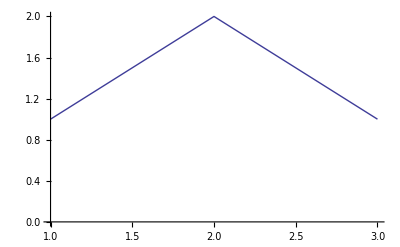
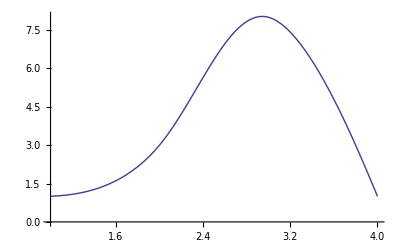
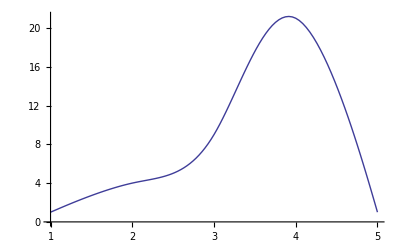
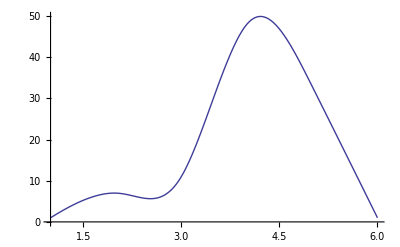
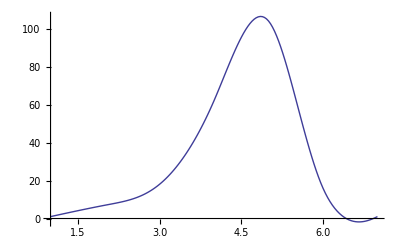
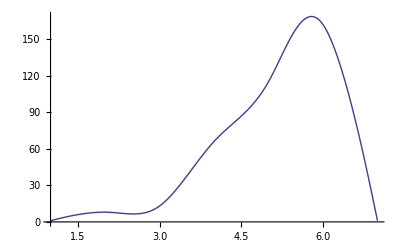
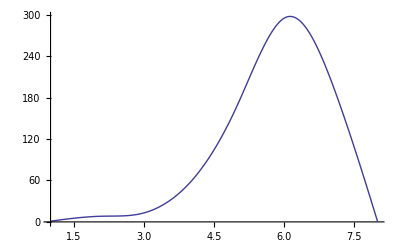

```mathematica
Analysis

L3:={1,4,5};
L4:={1,3,11,18};
L5:={1,4,9,31,51};
L6:={1,7,11,48,83,115};
L71:={1,7,18,62,104,244,259};
L72:={1,8,13,66,115,254,415};
L8:={1,8,13,58,169,295,831,1036};

listinfo[lis_]:=Module[{l2={},mid=(lis[[1]]+Last[lis])/2},
For[i=1,i≤Length[lis],i++,
AppendTo[l2,mid-Abs[ mid-lis[[i]]]];
];
l2
];
ListPlot[listinfo[#],Joined->True,InterpolationOrder->3]&/@{L3,L4,L5,L6,L71,L72,L8}
```

```mathematica
GenList[a_,b_,ra_,rb_,len_]:=Module[{list={1},i,p},
p=Mod[len,2];
For[i=1,i<len,i=i+2,
AppendTo[list,Floor[a*(ra^(Floor[(i-1)/2]))]];
];
For[i=2,i<len,i=i+2,
AppendTo[list,Floor[b*(rb^(Floor[(i-2)/2]))]];
];
DeleteDuplicates[Sort[list]]
];
```

```mathematica
Flist4:=GenList[5,17,2.6,2.6,7];
Print[Flist4];
For[i=4,i≤5,i++,
Print[i->CheckPSP[i][Flist4[[1;;i]]]];]
```

{1,5,13,17,33,44,114}

4→8

5→41